```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Nustore Files/Nutstore/PDF Euclidean Lattice/Hadron_Structure_Lattice/PDF/JURECA

```mathematica
<<myPackage`
```

```mathematica
πh5file="pion_2pt_0_70_JURECA.h5";
```

```mathematica
πh5NoSmrfile="pion_2pt_no_smr_A.h5";
```

```mathematica
πtags=Import[πh5file];
```

```mathematica
πNoSmrTags=Import[πh5NoSmrfile];
```

```mathematica
πPntSnkTags=Select[πtags,StringContainsQ[#,"TwoPnt_pnt_snk"]&];
```

```mathematica
πSnkSmrTags=Select[πtags,StringContainsQ[#,"TwoPnt_snk_smr"]&];
```

```mathematica
πPntSnkReTags=Select[πPntSnkTags,StringContainsQ[#,"Re"]&];
```

```mathematica
πPntSnkImTags=Select[πPntSnkTags,StringContainsQ[#,"Im"]&];
```

```mathematica
pPntSnkTags=Select[tags,StringContainsQ[#,"TwoPnt_pnt_snk"]&];
```

```mathematica
pPntSnkReTags=Select[pPntSnkTags,StringContainsQ[#,"Re"]&];
```

```mathematica
pPntSnkImTags=Select[pPntSnkTags,StringContainsQ[#,"Im"]&];
```

```mathematica
πPntSnkReTags⟦1⟧
```

/Mpi270-L32-T96_cfg_1000.lime/2.000000 20/TwoPnt_pnt_snk/Re

```mathematica
Select[πPntSnkReTags]
```

```mathematica
πCfPntSnk=Table[Import[πh5file,{"Datasets","/Mpi270-L32-T96_cfg_"<>ToString[i]<>".lime/"<>SmrPrmtrs⟦1⟧<>"/TwoPnt_pnt_snk/Re"}],{i,1000,1070}];
```

```mathematica
πSnkSmrTags
```

```mathematica
SmrPrmtrs=Flatten[Outer[StringJoin,Table[ToString[NumberForm[i,{1,6}]],{i,2,5}],Table[" "<>ToString[i],{i,20,50,10}]]]
```

{2.000000 20,2.000000 30,2.000000 40,2.000000 50,3.000000 20,3.000000 30,3.000000 40,3.000000 50,4.000000 20,4.000000 30,4.000000 40,4.000000 50,5.000000 20,5.000000 30,5.000000 40,5.000000 50}

```mathematica
πCf=Import[πh5file,{"Datasets",πPntSnkReTags⟦1⟧}];
```

```mathematica
πCfLst=myParallelTable[Import[πh5file,{"Datasets",πPntSnkReTags⟦i⟧}],{i,1,Length[πPntSnkReTags]}];
```

$Aborted

```mathematica
pCf=Import[ph5file,{"Datasets",pPntSnkReTags⟦1⟧}];
```

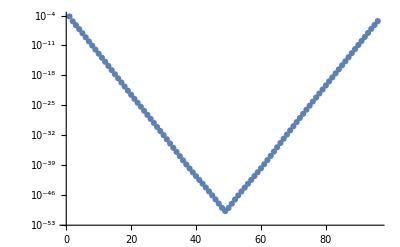

```mathematica
ListLogPlot[Import[πh5file,{"Datasets",πPntSnkReTags⟦20⟧}]]
```

```mathematica
(Cosh[2.2(t-48)]/.t->Range[1,96])/πCf
```

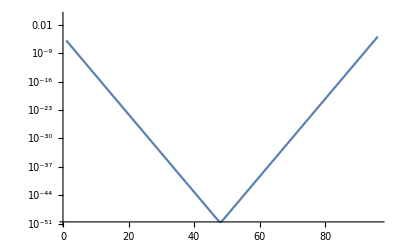

```mathematica
LogPlot[1/(32*10^49)Cosh[2.2(t-48)],{t,1,96}]
```

```mathematica
Cf⟦2;;-3⟧//Length
```

93

```mathematica
Cf⟦3;;-2⟧//Length
```

93

```mathematica
Cf⟦2;;-2⟧//Length
```

94

```mathematica
datas1=Table[ArcCosh[(#⟦t-1⟧+#⟦t+1⟧)/(2#⟦t⟧)],{t,2,95}]&/@πCfPntSnk;
```

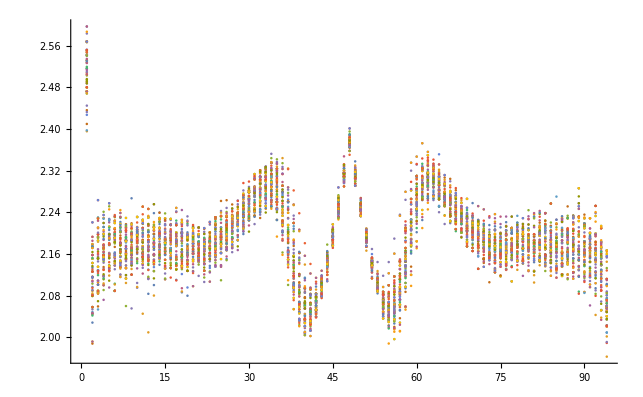

```mathematica
ListPlot[datas1,PlotRange->All]
```

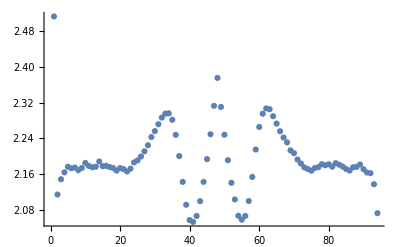

```mathematica
ListPlot[datas1//Mean]
```

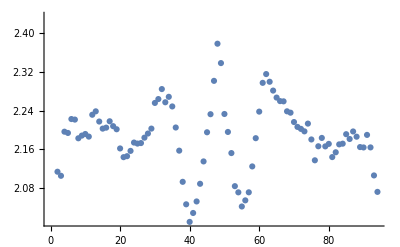

```mathematica
ListPlot[Table[ArcCosh[(πCf⟦t-1⟧+πCf⟦t+1⟧)/(2πCf⟦t⟧)],{t,2,95}]]
```

```mathematica
<<Units`
```

```mathematica
2.2*197
```

433.4

```mathematica
0.169/0.125*197
```

266.344

```mathematica
"/pions/piPlus(all)_piPlus(point(x0y0z0t0))"//InputForm
```

"/pions/piPlus(all)_piPlus(point(x0y0z0t0))"

```mathematica
?Total
```

Total[list] gives the total of the elements in list. 
Total[list,n] totals all elements down to level n. 
Total[list,{n}] totals elements at level n. 
Total[list,{n_1,n_2}] totals elements at levels n_1 through n_2.

```mathematica
Evanπ=Import["~//gauge.hdf5",{"Datasets","/pions/piPlus(all)_piPlus(point(x0y0z0t0))"}];
```

```mathematica
1/8 Table[ParallelSum[Evanπ⟦t,x,y,z,1⟧,{x,4},{y,4},{z,4}],{t,1,32}]
```

{0.11923,0.0062796,0.00063109,0.0000791692,0.0000103735,1.37124×10^-6,1.88544×10^-7,2.64208×10^-8,3.76016×10^-9,5.45321×10^-10,7.59854×10^-11,1.04339×10^-11,1.4817×10^-12,1.99982×10^-13,2.69228×10^-14,4.04876×10^-15,1.27203×10^-15,4.25428×10^-15,2.83956×10^-14,1.88001×10^-13,1.22934×10^-12,8.14345×10^-12,5.67931×10^-11,3.5471×10^-10,2.42656×10^-9,1.88869×10^-8,1.4757×10^-7,1.16328×10^-6,9.96999×10^-6,0.000088447,0.000719637,0.0066975}

```mathematica
Evanπ//Dimensions
```

{32,4,4,4,2}

```mathematica
πh5NoSmrfile="pion_2pt_no_smr_A.h5";
```

```mathematica
πNoSmrTags=Import[πh5NoSmrfile];
```

```mathematica
πNoSmrReTags=Select[πNoSmrTags,StringContainsQ[#,"Re"]&];
```

```mathematica
πNoSmrCF=Table[Import[πh5NoSmrfile,{"Datasets",πNoSmrReTags⟦i⟧}],{i,1,Length[πNoSmrReTags]}];
```

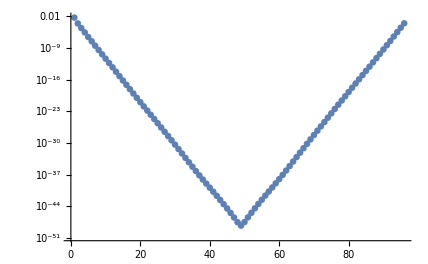

```mathematica
ListLogPlot[πCfPntSnk⟦1⟧]
```

```mathematica
πNoSmrCFp=πNoSmrCF⟦All,1;;48⟧~Join~(Reverse/@(πNoSmrCF⟦All,49;;-1⟧));
```

```mathematica
πNoSmrCFp//Dimensions
```

{174,48}

```mathematica
ListLogPlot[πNoSmrCF⟦All,1;;48⟧]
```

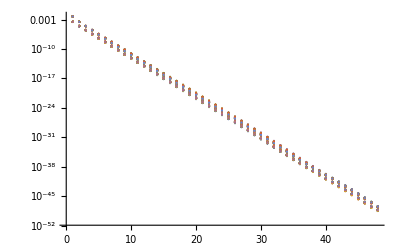

```mathematica
ListLogPlot[πNoSmrCFp]
```

```mathematica
data=Table[πNoSmrCFp⟦i,2;;-1⟧/πNoSmrCFp⟦i,1;;-2⟧,{i,1,Length[πNoSmrCFp]}];
```

```mathematica
dataMn=Mean[Table[πNoSmrCFp⟦i,2;;-1⟧/πNoSmrCFp⟦i,1;;-2⟧,{i,1,Length[πNoSmrCFp]}]]
```

{0.0764147,0.102191,0.105601,0.109524,0.110632,0.110835,0.111924,0.11267,0.113436,0.112355,0.112938,0.11349,0.113018,0.112792,0.113049,0.113437,0.113612,0.113713,0.114076,0.113949,0.113896,0.113895,0.113084,0.111865,0.11053,0.109504,0.107841,0.106433,0.104684,0.102998,0.101378,0.100598,0.101027,0.102927,0.106868,0.112633,0.118928,0.123941,0.126413,0.126136,0.12354,0.119013,0.113536,0.10765,0.101147,0.0953075,0.133774}

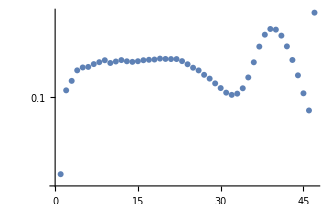

```mathematica
ListLogPlot[dataMn]
```

```mathematica
πNoSmrCF//Dimensions
```

{87,96}

```mathematica
πNoSmrCF//Length
```

87

```mathematica
MπEffNoSmr=ParallelTable[ArcCosh[(πNoSmrCF⟦i,t-1⟧+πNoSmrCF⟦i,t+1⟧)/(2πNoSmrCF⟦i,t⟧)],{i,1,87},{t,2,95}];
```

```mathematica
MπEffNoSmr//Dimensions
```

{87,94}

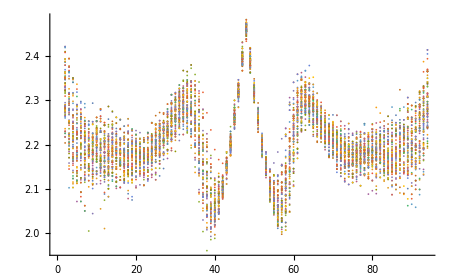

```mathematica
ListPlot[MπEffNoSmr]
```